```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get[FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels", "red.wl"}]];
(*Formatting functions-apply subscripts only when displaying*)prF[expr_]:=expr/. {i1->Subscript[i,1],i2->Subscript[i,2],r1->Subscript[r,1],r2->Subscript[r,2],y1->Subscript[i,21],y2->Subscript[i,12],be1->Subscript[β,1],be2->Subscript[β,2],ga1->Subscript[γ,1],ga2->Subscript[γ,2],th1->Subscript[θ,1],th2->Subscript[θ,2],th3->Subscript[θ,3],et1->Subscript[η,1],et2->Subscript[η,2],mu1->Subscript[μ,1],mu2->Subscript[μ,2],si1->Subscript[σ,1],si2->Subscript[σ,2],La->Λ,mu->μ};
RHS={La-be1 i1 s-be2 i2 s-mu s+r1 th1+r2 th2+R th3-be1 et1 s y1-be2 et2 s y2,-ga1 i1-i1 mu1+be1 i1 s+be1 et1 s y1,-ga2 i2-i2 mu2+be2 i2 s+be2 et2 s y2,ga1 i1-mu r1-be2 i2 r1 si2-r1 th1-be2 et2 r1 si2 y2,ga2 i2-mu r2-be1 i1 r2 si1-r2 th2-be1 et1 r2 si1 y1,be2 i2 r1 si2-ga2 y2-mu2 y2+be2 et2 r1 si2 y2,be1 i1 r2 si1-ga1 y1-mu1 y1+be1 et1 r2 si1 y1,-mu R-R th3+ga1 y1+ga2 y2};
var = {s, i1, i2, r1, r2,y2,y1,R};

cmu={mu2->mu,mu1->mu,th3->0};
Print["verif sum=",Total[RHS/.cmu]//FullSimplify];
{RN, rts, spe, alp, bet, gam} = ODE2RN[RHS, var];
Print["verif RHS-gam.rts=",gam.rts-RHS//Simplify];
Print[RN // Length," reactions and transitions: ",Transpose[{RN,rts}//prF]
//MatrixForm];
Print["minSiph=", mSi=minSiph[spe,RN][[1]]];
(* MAXIMAL ELIMINABLE SETS *)
{maxId, maxSets} = maxElim[RN, rts, var];
Print["reduced models are",maxSets];
{RHS,var,par,cp,mSi,Jx,Jy,cDFE,E0,K,R0A,infVars,ng}=bdAn[RN,rts,var];
Print["RHS=",RHS//FullSimplify//prF//MatrixForm," cE0=",E0//prF," reproduction funcs=",R0A//prF]
{RHS, var, par, cp, mSi, Jx, Jy, cDFE, E0, K, R0A, infVars, EA} = bdCom[RN, rts, var];

Print[  EA // Length," non DFE bd pts:"];cE1=EA[[2]][[1]];cE2=EA[[1]][[1]];
Print["E1=",E1];Print[" E2=",E2];

Print[" K= ",K//MatrixForm,"where the order is ",infV," after permutation ",K[[{1,3,2,4},{1,3,2,4}]]//MatrixForm, "the repr. funs are",R0A];
```

verif sum=La-mu (i1+i2+R+r1+r2+s+y1+y2)

verif RHS-gam.rts={0,0,0,0,0,0,0,0}

24 reactions and transitions: (0→s | Λ
r1→s | r_1 θ_1
r2→s | r_2 θ_2
r→s | R θ_3
i1+s→2 i1 | s i_1 β_1
s+y1→i1+y1 | s i_21 β_1 η_1
i2+s→2 i2 | s i_2 β_2
s+y2→i2+y2 | s i_12 β_2 η_2
i1→r1 | i_1 γ_1
i2→r2 | i_2 γ_2
i2+r1→i2+y2 | i_2 r_1 β_2 σ_2
r1+y2→2 y2 | i_12 r_1 β_2 η_2 σ_2
i1+r2→i1+y1 | i_1 r_2 β_1 σ_1
r2+y1→2 y1 | i_21 r_2 β_1 η_1 σ_1
y1→r | i_21 γ_1
y2→r | i_12 γ_2
s→0 | s μ
i1→0 | i_1 μ_1
i2→0 | i_2 μ_2
r1→0 | μ r_1
r2→0 | μ r_2
y2→0 | i_12 μ_2
y1→0 | i_21 μ_1
r→0 | R μ)

minSiph={{i1,y1},{i2,y2}}

reduced models are{{i1,i2,y2,y1,R},{s,r1,r2,R},{i1,r1,y1,R},{i2,r2,y2,R}}

RHS=(Λ-s (μ+i_2 β_2+β_1 (i_1+i_21 η_1)+i_12 β_2 η_2)+r_1 θ_1+r_2 θ_2+R θ_3
s i_21 β_1 η_1-i_1 (-s β_1+γ_1+μ_1)
s i_12 β_2 η_2-i_2 (-s β_2+γ_2+μ_2)
i_1 γ_1-r_1 (μ+θ_1+β_2 (i_2+i_12 η_2) σ_2)
i_2 γ_2-r_2 (μ+θ_2+β_1 (i_1+i_21 η_1) σ_1)
-i_12 (γ_2+μ_2)+r_1 β_2 (i_2+i_12 η_2) σ_2
-i_21 (γ_1+μ_1)+r_2 β_1 (i_1+i_21 η_1) σ_1
i_21 γ_1+i_12 γ_2-R (μ+θ_3)) cE0={R→0,r_1→0,r_2→0,s→Λ/μ,i_1→0,i_2→0,i_21→0,i_12→0} reproduction funcs={(β_1 (s+r_2 η_1 σ_1))/(γ_1+μ_1),(β_2 (s+r_1 η_2 σ_2))/(γ_2+μ_2)}

2 non DFE bd pts:

E1=E1

E2=E2

K= ((be1 s)/(ga1+mu1) | 0 | (be1 et1 s)/(ga1+mu1) | 0
0 | (be2 s)/(ga2+mu2) | 0 | (be2 et2 s)/(ga2+mu2)
(be1 r2 si1)/(ga1+mu1) | 0 | (be1 et1 r2 si1)/(ga1+mu1) | 0
0 | (be2 r1 si2)/(ga2+mu2) | 0 | (be2 et2 r1 si2)/(ga2+mu2))where the order is infV after permutation ((be1 s)/(ga1+mu1) | (be1 et1 s)/(ga1+mu1) | 0 | 0
(be1 r2 si1)/(ga1+mu1) | (be1 et1 r2 si1)/(ga1+mu1) | 0 | 0
0 | 0 | (be2 s)/(ga2+mu2) | (be2 et2 s)/(ga2+mu2)
0 | 0 | (be2 r1 si2)/(ga2+mu2) | (be2 et2 r1 si2)/(ga2+mu2))the repr. funs are{(be1 (s+et1 r2 si1))/(ga1+mu1),(be2 (s+et2 r1 si2))/(ga2+mu2)}

```mathematica
bdfp=bdFp[RHS,var,mSi];
Print["rat sols on  siphon faces are"]
bd1=bdfp[[1,1]]//FullSimplify
bd2=bdfp[[2,1]]//FullSimplify
```

rat sols on  siphon faces are

{i_1→0,i_21→0,i_2→((be2 La-mu (ga2+mu2)) (mu+th2))/(be2 mu (ga2+mu2)+be2 mu2 th2),R→0,r_1→0,r_2→(be2 ga2 La-ga2 mu (ga2+mu2))/(be2 mu (ga2+mu2)+be2 mu2 th2),s→(ga2+mu2)/be2,i_12→0}

{i_2→0,i_12→0,i_1→((be1 La-mu (ga1+mu1)) (mu+th1))/(be1 mu (ga1+mu1)+be1 mu1 th1),R→0,r_1→(be1 ga1 La-ga1 mu (ga1+mu1))/(be1 mu (ga1+mu1)+be1 mu1 th1),r_2→0,s→(ga1+mu1)/be1,i_21→0}

```mathematica
(* REPRODUCTION and INVASION  NUMBERS *)

R10 = R0A[[1]] /. E0 ;
R20 = R0A[[2]] /. E0 ;
R12 = R0A[[1]] /.  cE2;
R21 = R0A[[2]] /. cE1;
Print["R1(E0)=", R10, " R2(E0)=", R20, " R1(E2)=", R12, " R2(E1)=", R21]
cp=Thread[par>0];

Print["conjectured coexistence when"];
BIC=Reduce[And@@cp&&R10>1&&R20>1&&R12>1&&R21>1];
BICs=FullSimplify[BIC,cp];BICs//prF
coP=FindInstance[BIC,par][[1]]
```

R1(E0)=(be1 La)/(mu (ga1+mu1)) R2(E0)=(be2 La)/(mu (ga2+mu2)) R1(E2)=(be1 ((ga2+mu2)/be2+(et1 ga2 (be2 La-ga2 mu-mu mu2) si1)/(be2 (ga2 mu+mu mu2+mu2 th2))))/(ga1+mu1) R2(E1)=(be2 ((ga1+mu1)/be1+(et2 ga1 (be1 La-ga1 mu-mu mu1) si2)/(be1 (ga1 mu+mu mu1+mu1 th1))))/(ga2+mu2)

conjectured coexistence when

Λ β_2>μ (γ_2+μ_2)&&(((μ (γ_1+μ_1))/Λ<β_1<(β_2 (γ_1+μ_1))/(γ_2+μ_2)&&η_1>((μ γ_2+(μ+θ_2) μ_2) (-β_2 (γ_1+μ_1)+β_1 (γ_2+μ_2)))/(β_1 γ_2 (-Λ β_2+μ (γ_2+μ_2)) σ_1))||β_2 (γ_1+μ_1)==β_1 (γ_2+μ_2)||(β_1 (γ_2+μ_2)>β_2 (γ_1+μ_1)&&η_2>((μ γ_1+(μ+θ_1) μ_1) (β_2 (γ_1+μ_1)-β_1 (γ_2+μ_2)))/(β_2 γ_1 (-Λ β_1+μ (γ_1+μ_1)) σ_2)))

{be1→17,be2→54,et1→34,et2→10,ga1→3,ga2→33,La→73,mu→9,mu1→57,mu2→46,si1→48,si2→23,th1→13,th2→23,th3→27}

```mathematica
gridRes=50;plotInd={1,2};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[(*Step 3:Scanning-now with mSi from step 1*)
{plot,noSol,results}=scan[RHS,var,par,coP,plotInd,mSi,(*mSi auto-provided*)gridRes,steTol,staTol,choTol,R10,R20,R12,R21];]
plot
```

```mathematica
(*E1*)
cE2=bd1[[2]]
cE1=bdfp[[2,1]][[2]]
jac=Grad[RHS,var];
j1=jac/.cE1/.{i2->0,y2->1}//FullSimplify;
cChu={et1->1,et2->1,th3->0,th1->0,th2->0,La->mu};
Print[" At cE1, chp of jac, ch1, factorizes as"]
ch1=Numerator[Together[CharacteristicPolynomial[j1,u]/.cChu]]//Factor
(*{lSta,qSta,hDeg,ll,ql}=sta[ch1,par];
Print["Stability of E1 holds iff"]
re1=Reduce[Join[cp,lSta,qSta]]//FullSimplify*)
```

{i_2→((β_2 Λ-μ (γ_2+μ)) (μ+θ_2))/(β_2 μ (γ_2+μ+θ_2)),R→0,r_1→0,r_2→(β_2 γ_2 Λ-γ_2 μ (γ_2+μ))/(β_2 μ (γ_2+μ+θ_2)),s→(γ_2+μ)/β_2,y_2→0}

{i_1→((β_1 Λ-γ_1 μ-μ^2) (μ+θ_1))/(β_1 μ (γ_1+μ+θ_1)),R→0,r_1→(γ_1 (β_1 Λ-γ_1 μ-μ^2))/(β_1 μ (γ_1+μ+θ_1)),r_2→0,s→(γ_1+μ)/β_1,y_1→0}

At cE1, chp of jac, ch1, factorizes as

Stability of E1 holds iff

β_1>0&&β_2>0&&η_1>0&&η_2>0&&γ_1>0&&γ_2>0&&Λ>0&&μ>0&&σ_1>0&&σ_2>0&&θ_1>0&&θ_2>0&&θ_3>0

Auto-determined varInd: {1,2,5}

Susceptible: s

Strain 1 (first compartment): i_1

Strain 2 (first compartment): i_2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 2., β_2 = 2.

Adjusted ranges: β_1 ∈ [0.001, 8.], β_2 ∈ [0.001, 6.]

Scanning 2500 parameter combinations...

Checked 730 potential coexistence points

All Rij equations: {β_1/2==1,β_2/2==1,((3+β_1) β_2)/(5 β_1)==1,(β_1 (4+β_2))/(6 β_2)==1}

DFE: 221 (9%)

E2: 612 (24%)

E1: 937 (37%)

EE-Stable: 713 (29%)

NoSol: 17 (1%)

{7.26563,Null}

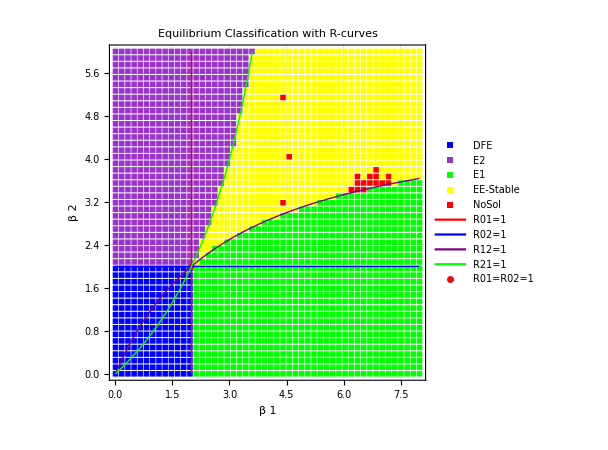

```mathematica
gridRes=50;plotInd={1,2};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[(*Step 3:Scanning-now with mSi from step 1*)
{plot,noSol,results}=scan[RHS,var,par,coP,plotInd,mSi,(*mSi auto-provided*)gridRes,steTol,staTol,choTol,R01,R02,R12,R21];]
plot
```